```mathematica
hullcurve = 2*Abs[x/2]^3
hull = (x≥-2&&x≤2&&y≥0&&y≤10&&z≥hullcurve&&z≤2)
hullreg = ImplicitRegion[True,{{x,-2,2},{y, 0, 10}, {z, hullcurve, 2}}]
hulldensity = 300
waterdensity = 1000
ballastdensity = 5000000/(81*π)
ballast = ImplicitRegion[x^2+(z-0.09)^2≤0.09^2&&y≥0&&y≤10, {x,y,z}]
boatdens = Piecewise[{{ballastdensity+hulldensity, {x,y,z}∈ballast}}, hulldensity]
Show[RegionPlot3D[hullreg,PlotStyle->Directive[Yellow,Opacity[0.5]],Mesh->None], RegionPlot3D[ballast, PlotStyle->Directive[Blue,Opacity[0.5]],Mesh->None]]
```

Abs[x]^3/4

x≥-2&&x≤2&&y≥0&&y≤10&&z≥Abs[x]^3/4&&z≤2

ImplicitRegion[-2≤x≤2&&0≤y≤10&&Abs[x]^3/4≤z≤2,{x,y,z}]

300

1000

5000000/(81 π)

ImplicitRegion[x^2+(-0.09+z)^2≤0.0081&&y≥0&&y≤10,{x,y,z}]

Piecewise[{{300+5000000/(81 π), {x,y,z}∈ImplicitRegion[x^2+(-0.09+z)^2≤0.0081&&y≥0&&y≤10,{x,y,z}]}, {300, True}}]

-Graphics3D-

```mathematica
Waterline[θ_]:= ImplicitRegion[z≤Tan[30*π/180]*x+draft,{{x,-2,2}, {y,0,10}, {z,0,2}}]
Mass[boatregion_, boatdensity_]:=Integrate[boatdensity,{x, y, z}∈boatregion]
CenterOfMass[boatregion_, boatdensity_]:= 1/Mass[boatregion, boatdensity]*Integrate[boatdensity * {x,y,z}, {x,y,z}∈boatregion]
CalculateDraft[boatregion_, boatdensity_, θ_]:=NSolve[Integrate[1, {x,y,z}∈RegionIntersection[boatregion, Waterline[θ]]]==Mass[boatregion, boatdensity]/1000, draft][[1]]
DisplacedWater[boatregion_, boatdensity_, θ_]:= RegionIntersection[boatregion, Waterline[θ]]/.CalculateDraft[boatregion, boatdensity, θ]
CenterOfBuoyancy[boatregion_, boatdensity_, θ_]:=1000/Mass[boatregion, boatdensity] * Integrate[{x,y,z}, {x,y,z}∈DisplacedWater[boatregion, boatdensity, θ]]
RightingMoment[boatregion_, boatdensity_, θ_]:=Cross[CenterOfBuoyancy[boatregion, boatdensity, θ]-CenterOfMass[boatregion, boatdensity], Mass[boatregion, boatdensity]*9.8*{-Sin[θ*π/180], 0, Cos[θ*π/180]}]
```

RightingMoment successfully calculates the vector torque exerted by the water on a boat with a hull shape defined by a given region, density as a given function of {x,y,z}, and a given heel angle. Units are in kg and m, to convert to cm and g replace any instance of the number 1000 with the number 1.

Plot of righting moment versus angle for boat from 0 to 180 degrees. The function returns a table of x y and z values for torque every 5 degrees and then fits a 5th degree polynomial (adding more degrees did not change result) and then finds this polynomial’s root to find when torque is zero. It returns the max torque and the angle it occurs as well as the avs.

```mathematica
f[angle_]:=RightingMoment[hullreg, boatdens,angle]
angleTable=Table[f[angle],{angle,0,180,5}];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

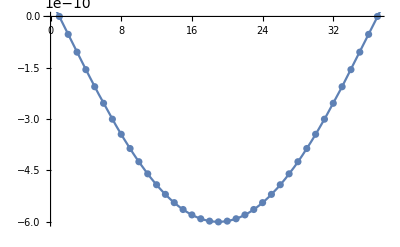

{5.07701×10^-11,{x→0.}}

185.049

```mathematica
bestFit=Fit[angleTable[[All,3]],{1,x,x^2,x^3,x^4,x^5},x];
Plot[bestFit,{x,0,180}];
ListPlot[angleTable[[All,3]]];
Show[%,%%]
root=FindRoot[bestFit,{x,30}];
maxTorque=FindMinimum[bestFit,{x,0}]
avs=root[[1,2]]*5
```

Below I did it for all 3 axes but the equation returns some wonky results for those values so we should look into that later. Mostly ignore that stuff for now.

3D righting curves we can use later with two angles:

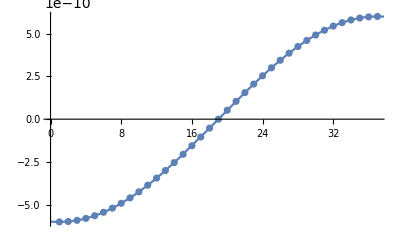

{-5.98537×10^-10,{x→0.}}

-92.5291

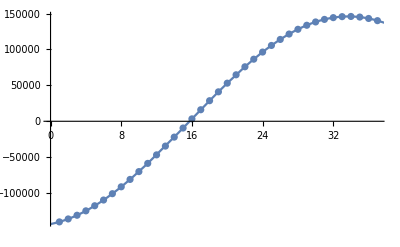

{-145912.,{x→-2.22621}}

78.687

-Graphics-

{x→37.0099}

{5.07701×10^-11,{x→0.}}

185.049

```mathematica
bestFitx=Fit[angleTable[[All,1]],{1,x,x^2,x^3,x^4,x^5},x];
Plot[bestFitx,{x,0,180}];
ListPlot[angleTable[[All,1]]];
Show[%,%%]
rootx=FindRoot[bestFitx,{x,0}];
maxTorquex=FindMinimum[bestFitx,{x,0}]
avsx=rootx[[1,2]]*5
bestFity=Fit[angleTable[[All,2]],{1,x,x^2,x^3,x^4,x^5},x];
Plot[bestFity,{x,0,180}];
ListPlot[angleTable[[All,2]]];
Show[%,%%]
rooty=FindRoot[bestFity,{x,0}];
maxTorquey=FindMinimum[bestFity,{x,0}]
avsy=rooty[[1,2]]*5
bestFitz=Fit[angleTable[[All,3]],{1,x,x^2,x^3,x^4,x^5},x];
Plot[bestFitz,{x,0,180}];
ListPlot[angleTable[[All,3]]];
Show[%,%%]
rootz=FindRoot[bestFitz,{x,30}]
maxTorquez=FindMinimum[bestFitz,{x,0}]
avsz=rootz[[1,2]]*5
```